# CKT Classic

## Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Miguel\Github\Chaotic_eigenfunctions\QKT\Poincare

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

```mathematica
Clear[F,Fun,Funinv];
F[α_,k_,s_]:=Module[{a,sx=s[[1]]},
{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}}
];
Fun[α_,k_,s_]:=Module[{sx=s[[1]]},
{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}}.s
];
Funinv[α_,k_,s_]:=Module[{sx=s[[1]]},
MatrixPower[{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}},-1].s
];
Clear[change];
change[s_]:=Module[{B=Sqrt[2/(1-s[[3]])]},
{s[[1]]*B,s[[2]]*B}
];

Clear[change2];
change2[Q_]:=Module[{B=Norm[Q]},
{Q[[1]]*Sqrt[1-(1/4)B^2],Q[[2]]*Sqrt[1-(1/4)B^2],(1/2)B^2 -1}
];

Clear[mapeo];
mapeo[Qini_,α_,k_,n_]:=Module[{list,s={Qini[[1]]*Sqrt[1-(1/4)Norm[Qini]^2],Qini[[2]]*Sqrt[1-(1/4)Norm[Qini]^2],(1/2)Norm[Qini]^2 -1}},
list=NestList[Fun[α,k,#]&,s,n];
Map[change[#]&,list]
];

Clear[mapeoinv];
mapeoinv[Qini_,α_,k_,n_]:=Module[{list,s={Qini[[1]]*Sqrt[1-(1/4)Norm[Qini]^2],Qini[[2]]*Sqrt[1-(1/4)Norm[Qini]^2],(1/2)Norm[Qini]^2 -1}},
list=NestList[Funinv[α,k,#]&,s,n];
Map[change[#]&,list]
];

mapeob[Qini_,α_,k_,n_]:=Module[{map={},snew,a,s,Qnew},
AppendTo[map,Qini];
s=change2[Qini];
Do[
snew=MatrixPower[N[F[α,k,s]],2].s;
AppendTo[map,change[snew]];
s=snew;
,{l,1,n}];
map
];

Clear[Jx,Jy,Jz,M,mapeo1,jmas];
Jx[x_,y_,z_,α_,k_]:=x*Cos[α]-y*Sin[α]*Cos[k*x]+z*Sin[α]*Sin[k*x];
Jy[x_,y_,z_,α_,k_]:=x*Sin[α]+y*Cos[α]*Cos[k*x]-z*Cos[α]*Sin[k*x];
Jz[x_,y_,z_,α_,k_]:=y*Sin[k*x]+z*Cos[k*x];

M[Jini_,α_Real,k_Real]:=Module[{M},
M={{D[Jx[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jx[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jx[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}},
{D[Jy[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jy[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jy[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}},{D[Jz[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jz[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jz[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}}}//N;
M
];

mapeo1[si_,α_,k_,n_]:=Module[{s=si},
MatrixPower[F[α,k,s],n].s
];
```

```mathematica
F[α_,k_,s_]:=Module[{a,sx=s[[1]]},
{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}}
];
```

## Poincare differences

```mathematica
Clear[rot];
rot[theta_]:={{Cos[theta],-Sin[theta]},{Sin[theta],Cos[theta]}};
```

```mathematica
Clear[α];
α=GoldenRatio;
τ=1;
```

```mathematica
(*randomregion=RandomPoint[Disk[{0,0},1.999],350];*)
(*randomregion=RandomPoint[Disk[{-1.01,0.58},0.01],10];*)
randomregion=Table[{i,0},{i,0,1.999,0.02}];
θ=α/2;
randomregion=(rot[θ].#&/@randomregion);
randomregionb=(rot[θ+Pi/4].#&/@randomregion);
randomregion=Join[randomregion,randomregionb];
randomregiondos=Table[{0,i},{i,0,1.999,0.02}];
randomregion=Join[randomregion,randomregiondos];
randomregionc=-randomregion;
randomregion//Length
```

300

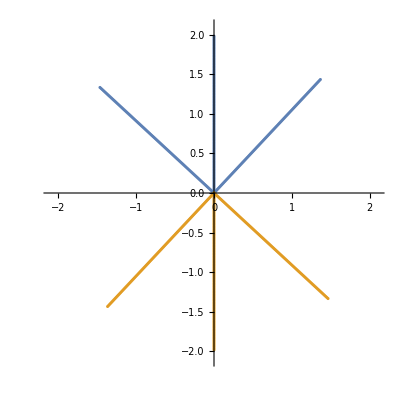

```mathematica
ListPlot[{randomregion,randomregionc},AspectRatio->1,PlotRange->{{-2.1,2.1},{-2.1,2.1}}]
```

```mathematica
kicks=1000;
```

```mathematica
α=GoldenRatio;
klist=Table[i,{i,α/20,40α,α/20}];
```

```mathematica
Do[

puntosa=ParallelTable[Quiet[mapeo[i,GoldenRatio,klist[[j]],kicks]],{i,randomregion}];
newpoincarea=ArrayReshape[puntosa,{Length[randomregion]*(kicks+1),2}];
poincarea=Graphics[{PointSize[0.0015],Blue,Opacity[0.1],Point[newpoincarea]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,PlotLabel->Row[{Style["α = ",45,Black],Style[N[α],45,Black],Style[", k = ",45,Black], Style[N[klist[[j]]],50,Black]}],FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->1000];

puntosa=ParallelTable[Quiet[mapeo[i,GoldenRatio,klist[[j]],kicks]],{i,randomregionc}];
newpoincarea=ArrayReshape[puntosa,{Length[randomregionc]*(kicks+1),2}];
poincareb=Graphics[{PointSize[0.0010],Red,Opacity[0.1],Point[newpoincarea]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,PlotLabel->Row[{Style["α = ",45,Black],Style[N[α],45,Black],Style[", k = ",45,Black], Style[N[klist[[j]]],50,Black]}],FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->1000];

Export["poincare_alfa_"<>ToString[N[α]]<>"_k_"<>ToString[N[klist[[j]]]]<>"_kicks_"<>ToString[kicks]<>"_frame"<>ToString[j]<>".png",Show[{poincarea,poincareb}]];
,{j,Length[klist]}]
```

$Aborted

```mathematica
filteredinitial//Length
```

103

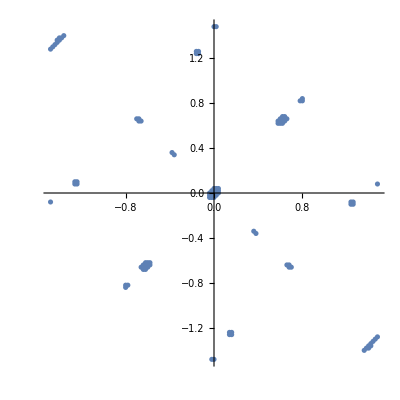

```mathematica
ListPlot[filteredinitial,AspectRatio->1]
```

```mathematica
α=GoldenRatio;
k=20.;
kicks=2000;
puntosa=ParallelTable[Quiet[mapeo[i,α,k,kicks]],{i,filteredinitial}];
newpoincarea=ArrayReshape[puntosa,{Length[randomregion]*(kicks+1),2}];
poincarea=Graphics[{PointSize[0.0015],Blue,Opacity[1],Point[newpoincarea]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,PlotLabel->Row[{Style["α = ",45,Black],Style[N[α],45,Black],Style[", k = ",45,Black], Style[N[20.],50,Black]}],FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->1000];
Export["poincare_filtered_alfa_"<>ToString[N[α]]<>"_k_"<>ToString[N[20.]]<>"_kicks_"<>ToString[kicks]<>"_frameb"<>ToString[248]<>".png",poincarea];
```

## Powers of Poincaré

```mathematica
Clear[Fun];
Fun[α_,k_,s_]:=Module[{sx=s[[1]]},
{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}}.s
];
(*Clear[Funp];
Funp[α_,k_,s_,p_]:=Module[{sx=s[[1]]},
MatrixPower[{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}},p].s
];*)
(*Clear[Funp];
Funp[α_,k_,s_,p_]:=Module[{mat=F[α,k,s],point=Fun[α,k,s],sx=s[[1]],a},
a=F[α,k,point];
MatrixPower[a.mat,p].s
];*)

(*Clear[Funp];
Funp[α_,k_,s_,p_]:=Module[{mat=F[α,k,s],point=Fun[α,k,s],sx=s[[1]],a,b},
a=F[α,k,point];
b=F[α,k,a.point];
MatrixPower[b.a.mat,p].s
];*)

Clear[Funp];
Funp[α_,k_,s_,p_]:=Module[{mat=F[α,k,s],point=Fun[α,k,s],sx=s[[1]],a,b,c},
a=F[α,k,point];
b=F[α,k,a.point];
c=F[α,k,b.(a.point)];
MatrixPower[c.b.a.mat,p].s
];

Clear[mapeop];
mapeop[Qini_,α_,k_,n_,p_]:=Module[{list,s={Qini[[1]]*Sqrt[1-(1/4)Norm[Qini]^2],Qini[[2]]*Sqrt[1-(1/4)Norm[Qini]^2],(1/2)Norm[Qini]^2 -1}},
list=NestList[Funp[α,k,#,p]&,s,n];
Map[change[#]&,list]
];
```

```mathematica
Clear[rot];
rot[theta_]:={{Cos[theta],-Sin[theta]},{Sin[theta],Cos[theta]}};
```

```mathematica
Clear[α];
α=Pi/2;
τ=1;
```

```mathematica
radius=1.99999;
delta=0.010;
xCoords=Range[-radius,radius,delta];
yCoords=Range[-radius,radius,delta];
gridPoints=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
(*boundaryPoints=(radius)Table[{Cos[i],Sin[i]},{i,0,2Pi,Pi/100}];*)
circlePoints=Select[gridPoints,Norm[#]<radius&];
(*randomregion=Join[boundaryPoints,circlePoints];
randomregionb=-randomregion;*)
randomregion=circlePoints;
randomregion//Length
```

125613

```mathematica
ListPlot[randomregion,AspectRatio->1,PlotRange->{{-2.1,2.1},{-2.1,2.1}}]
```

```mathematica
line=Table[{Rationalize[i],0},{i,0,1.999,0.0005}];
sym=ParallelTable[rot[α/3].i,{i,line}];
randomregion=sym;
```

```mathematica
randomregion//Length
```

125613

```mathematica
2*4^9
```

524288

```mathematica
kicks=256;
k=11.6;
p=524288;
```

```mathematica
puntosa=ParallelTable[Quiet[mapeop[i,α,k,kicks,p]],{i,randomregion}];
newpoincarea=ArrayReshape[puntosa,{Length[randomregion]*(kicks+1),2}];poincarec=Graphics[{PointSize[0.001],Blue,Opacity[0.05],Point[newpoincarea]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,PlotLabel->Row[{Style["α = ",45,Black],Style[α*τ,45,Black],Style[", k = ",45,Black], Style[k,50,Black],Style[", n = ",45,Black],Style[kicks,50,Black],Style[", p = ",45,Black],Style[p,50,Black]}],FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->1500];
Export["poincare_period_4_alfa_"<>ToString[N[α]]<>"_k_"<>ToString[k]<>"_kicks_"<>ToString[kicks]<>"_p_"<>ToString[p]<>".png",poincarec]
```

poincare_period_4_alfa_1.5708_k_11.6_kicks_256_p_524288.png

## Accumulation points

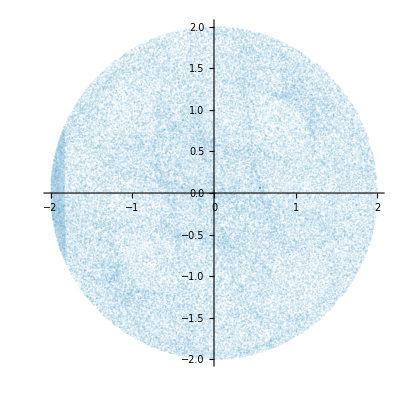

```mathematica
ListPlot[newpoincarea[[1;;100000]],AspectRatio->1,PlotStyle->Directive[Opacity[0.1]]]
```

```mathematica
data=newpoincarea[[1;;50000]];
```

```mathematica
(*---Step 1:Validate the Input Data---*)If[!(ListQ[data]&&AllTrue[data,MatchQ[#,{_Real,_Real}]&]),Print["Error: Data is not in the correct format. It should be a list of {x, y} points."];
Abort[]];
```

```mathematica
(*---Step 2:Compute KDE with Automatic Bandwidth Selection---*)
densityDist=SmoothKernelDistribution[data];

(*---Step 3:Define Grid Parameters---*)
gridStep=0.01;
{xMin,xMax}={-2,2}; (*Disk of radius 2*)
{yMin,yMax}={-2,2};

(*---Step 4:Generate Density Matrix in Parallel---*)
densityMatrix=ParallelTable[densityDist[x,y],{x,xMin,xMax,gridStep},{y,yMin,yMax,gridStep}];

(*---Step 5:Validate Density Matrix---*)
If[!MatrixQ[densityMatrix,NumericQ],Print["Error: densityMatrix is not valid. Check input data."];
Abort[]];

(*---Step 6:Convert Density Matrix to an Image---*)
densityImage=Image[densityMatrix,"Real"];

(*---Step 7:Detect Local Maxima---*)
maximaImage=MaxDetect[densityImage,0.001];

(*---Step 8:Extract Pixel Positions of Maxima---*)
maximaPixelPositions=Position[ImageData[maximaImage],1];

(*---Step 9:Convert Pixel Positions to (x,y) Coordinates---*)
maximaCoords=Table[{xMin+(col-1)*gridStep,yMax-(row-1)*gridStep},{{row,col}∈maximaPixelPositions}];

(*---Step 10:Ensure Numeric Validity---*)
maximaCoords=Select[maximaCoords,(NumericQ[#[[1]]]&&NumericQ[#[[2]]])&];

(*---Step 11:Refine Maxima Using FindMaximum (Parallelized)---*)
refinedMaximaCoords=ParallelMap[Function[pt,Quiet[Check[FindMaximum[densityDist[x,y],{{x,pt[[1]]},{y,pt[[2]]}}][[2]]//Values,pt (*Return original point if FindMaximum fails*)]]],maximaCoords];

(*---Final Output:refinedMaximaCoords contains (x,y) of accumulation points---*)
refinedMaximaCoords
```

Error: densityMatrix is not valid. Check input data.

$Aborted

```mathematica
12
```

12

## test

```mathematica
α=0.84;
```

```mathematica
line=Table[{Rationalize[i],0},{i,-1.999,1.999,0.1}];
lineb=Table[{0,Rationalize[i]},{i,-1.999,1.999,0.1}];
linec=Join[line,lineb];
sym=Table[rot[α/2].i,{i,line}];
sym=Join[sym,Table[rot[Pi/2].i,{i,sym}]];
randomregion=Join[linec,sym];
```

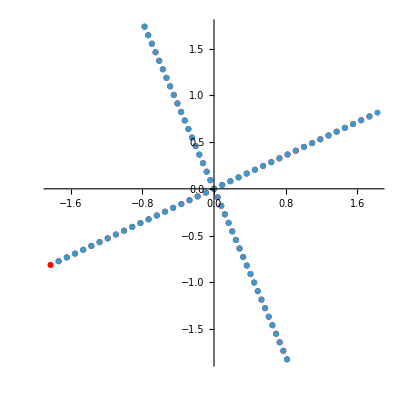

```mathematica
Show[{ListPlot[sym,PlotRange->All,AspectRatio->1,PlotStyle->Red],ListPlot[Table[rot[Pi/2].i,{i,sym}],PlotRange->All,AspectRatio->1]},PlotRange->All]
```

```mathematica
ListPointPlot3D[{Map[change2,sym],Map[change2,Table[rot[α/2].i,{i,sym}]]},PlotRange->All,BoxRatios->{1, 1, 1},AxesLabel->{Style["X",15,Black], Style["Y",15,Black],Style["Z",15,Black]},PlotLegends->Automatic]
```

-Graphics3D-

## Symmetry lines inverse

```mathematica
Clear[rot];
rot[theta_]:={{Cos[theta],-Sin[theta]},{Sin[theta],Cos[theta]}};
```

```mathematica
Clear[α];
α=Pi/2;
τ=1;
```

```mathematica
line=Table[{Rationalize[i],0},{i,-1.999,1.999,0.01}];
sym=ParallelTable[rot[α/2].i,{i,line}];
sym=Join[sym,Table[rot[Pi/2].i,{i,sym}]];
sym//Length
```

800

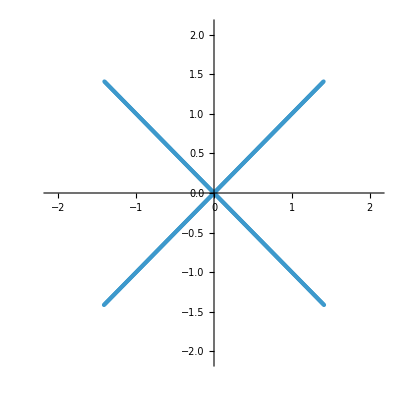

```mathematica
ListPlot[sym,AspectRatio->1,PlotRange->{{-2.1,2.1},{-2.1,2.1}}]
```

```mathematica
Clear[circleParam];
circleParam[t_]:={Cos[α/2]Cos[t], Sin[α/2]Cos[t],Sin[t]};
```

```mathematica
circle=Table[circleParam[i],{i,0,2Pi,0.0005}];
qpcircle=Map[change,circle];
qpcircle//Length
```

12567

```mathematica
n=5;
kicks=3000;
```

```mathematica
randomregion=RandomPoint[Disk[{0,0},1.999],200];
```

```mathematica
k=11.6;
puntosa=ParallelTable[Quiet[mapeo[i,α,k,kicks]],{i,randomregion}];
newpoincarea=ArrayReshape[puntosa,{Length[randomregion]*(kicks+1),2}];
poincare=Graphics[{PointSize[0.0015],Gray,Opacity[0.1],Point[newpoincarea]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,PlotLabel->Row[{Style["α = ",45,Black],Style[N[α],45,Black],Style[", k = ",45,Black], Style[N[k],50,Black]}],FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->1500];
```

```mathematica
k=11.6;
n=10;
(*puntos=ParallelTable[Quiet[mapeo[i,α,k,n]],{i,sym}];
puntosinv=ParallelTable[Quiet[mapeoinv[i,α,k,n]],{i,sym}];*)
puntos=ParallelTable[Quiet[mapeo[i,α,k,n]],{i,qpcircle}];
puntosinv=ParallelTable[Quiet[mapeoinv[i,α,k,n]],{i,qpcircle}];
```

```mathematica
Do[

symmetriesinv=Graphics[{PointSize[0.0015],Blue,Opacity[0.5],Point[puntosinv[[All,i]]]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,PlotLabel->Row[{Style["α = ",45,Black],Style[N[α],45,Black],Style[", k = ",45,Black], Style[N[k],50,Black]}],FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->1500];
symmetries=Graphics[{PointSize[0.0015],Red,Opacity[0.5],Point[puntos[[All,i]]]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,PlotLabel->Row[{Style["α = ",45,Black],Style[N[α],45,Black],Style[", k = ",45,Black], Style[N[k],50,Black]}],FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->1500];
Export["symmetry_alfab_"<>ToString[N[α]]<>"_k_"<>ToString[N[k]]<>"_n_"<>ToString[i]<>".png",Show[{symmetries,symmetriesinv}]];

,{i,n+1}];
```

```mathematica
newpoincareinv=ArrayReshape[puntosinv,{Length[sym]*(n+1),2}];
symmetriesinv=Graphics[{PointSize[0.0015],Blue,Opacity[0.08],Point[newpoincareinv]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,PlotLabel->Row[{Style["α = ",45,Black],Style[N[α],45,Black],Style[", k = ",45,Black], Style[N[k],50,Black]}],FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->1500];
newpoincare=ArrayReshape[puntos,{Length[sym]*(n+1),2}];
symmetries=Graphics[{PointSize[0.0015],Red,Opacity[0.08],Point[newpoincare]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,PlotLabel->Row[{Style["α = ",45,Black],Style[N[α],45,Black],Style[", k = ",45,Black], Style[N[k],50,Black]}],FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->1500];
Export["symmetry_forward_alfa_"<>ToString[N[α]]<>"_k_"<>ToString[N[k]]<>"_n_"<>ToString[n]<>"b.png",Show[{symmetries}]]
Export["symmetry_backward_alfa_"<>ToString[N[α]]<>"_k_"<>ToString[N[k]]<>"_n_"<>ToString[n]<>"b.png",Show[{symmetriesinv}]]
Export["symmetry_all_alfa_"<>ToString[N[α]]<>"_k_"<>ToString[N[k]]<>"_n_"<>ToString[n]<>"b.png",Show[{symmetries,symmetriesinv}]]
Export["symmetry_all_withpoincare_alfa_"<>ToString[N[α]]<>"_k_"<>ToString[N[k]]<>"_n_"<>ToString[n]<>"b.png",Show[{poincare,symmetries,symmetriesinv}]]
```

symmetry_forward_alfa_1.5708_k_11.6_n_10b.png

symmetry_backward_alfa_1.5708_k_11.6_n_10b.png

symmetry_all_alfa_1.5708_k_11.6_n_10b.png

symmetry_all_withpoincare_alfa_1.5708_k_11.6_n_10b.png

## Power eigenvalues

```mathematica
Clear[Fun];
Fun[α_,k_,s_]:=Module[{sx=s[[1]]},
{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}}.s
];
Clear[Funp];
Funp[α_,k_,s_,p_]:=Module[{sx=s[[1]]},
MatrixPower[{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}},p].s
];
(*Clear[Funp];
Funp[α_,k_,s_,p_]:=Module[{mat=F[α,k,s],point=Fun[α,k,s],sx=s[[1]],a},
a=F[α,k,point];
MatrixPower[a.mat,p].s
];*)

(*Clear[Funp];
Funp[α_,k_,s_,p_]:=Module[{mat=F[α,k,s],point=Fun[α,k,s],sx=s[[1]],a,b},
a=F[α,k,point];
b=F[α,k,a.point];
MatrixPower[b.a.mat,p].s
];*)

(*Clear[Funp];
Funp[α_,k_,s_,p_]:=Module[{mat=F[α,k,s],point=Fun[α,k,s],sx=s[[1]],a,b,c},
a=F[α,k,point];
b=F[α,k,a.point];
c=F[α,k,b.(a.point)];
MatrixPower[c.b.a.mat,p].s
];*)

Clear[mapeop];
mapeop[Qini_,α_,k_,n_,p_]:=Module[{list,s={Qini[[1]]*Sqrt[1-(1/4)Norm[Qini]^2],Qini[[2]]*Sqrt[1-(1/4)Norm[Qini]^2],(1/2)Norm[Qini]^2 -1}},
list=NestList[Funp[α,k,#,p]&,s,n];
Map[change[#]&,list]
];
```

```mathematica
Clear[rot];
rot[theta_]:={{Cos[theta],-Sin[theta]},{Sin[theta],Cos[theta]}};
```

```mathematica
Clear[α];
α=0.84;
τ=1;
```

```mathematica
radius=1.99999;
delta=0.035;
xCoords=Range[-radius,radius,delta];
yCoords=Range[-radius,radius,delta];
gridPoints=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
(*boundaryPoints=(radius)Table[{Cos[i],Sin[i]},{i,0,2Pi,Pi/100}];*)
circlePoints=Select[gridPoints,Norm[#]<radius&];
(*randomregion=Join[boundaryPoints,circlePoints];
randomregionb=-randomregion;*)
randomregion=circlePoints;
randomregion//Length
```

10251

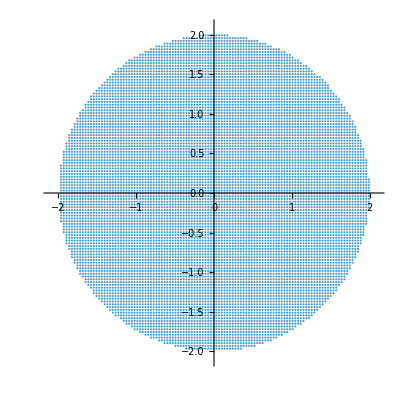

```mathematica
ListPlot[randomregion,AspectRatio->1,PlotRange->{{-2.1,2.1},{-2.1,2.1}}]
```

```mathematica
Clear[mat];
mat[α_,k_,{x_,y_,z_},p_]:=Module[{sx=x},
MatrixPower[{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}},p]
];
Clear[jac];
jac[Jini_,α_Real,k_Real,p_]:=Module[{M,jx=mat[α,k,{x,y,z},p][[1]].{x,y,z},jy=mat[α,k,{x,y,z},p][[2]].{x,y,z},jz=mat[α,k,{x,y,z},p][[3]].{x,y,z}},
M={{D[jx, x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[jx, y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[jx, z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}},
{D[jy, x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[jy, y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[jy, z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}},{D[jz, x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[jz, y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[jz, z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}}}//N;
M
];
```

```mathematica
k=20.;
```

```mathematica
eigenvalues=ParallelTable[Sort[Eigenvalues[jac[change2[i],α,k,1]]],{i,randomregion}];
```

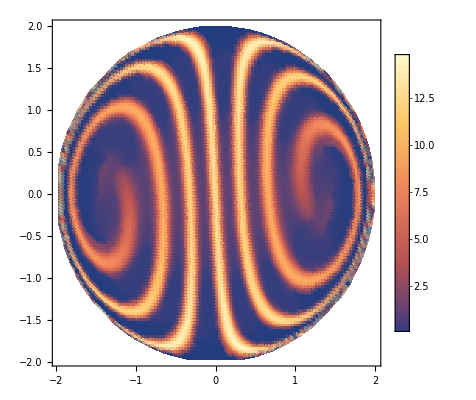

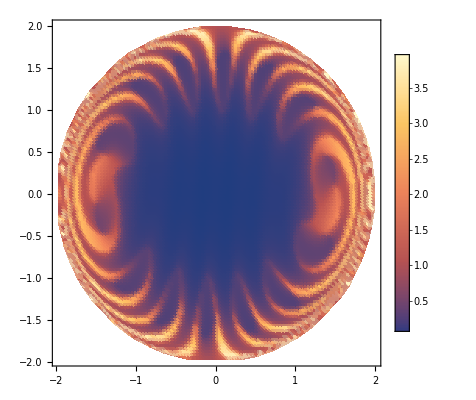

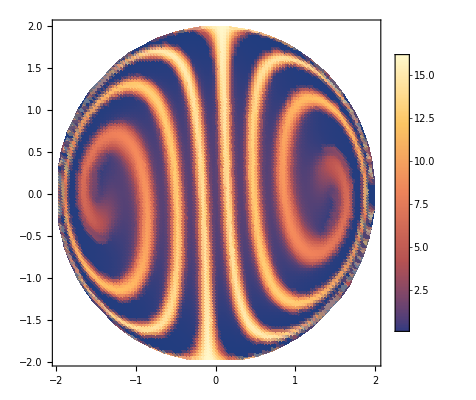

```mathematica
ListDensityPlot[Transpose[{randomregion[[All,1]],randomregion[[All,2]],Abs[eigenvalues[[All,1]]]}],PlotTheme->"Detailed",PlotRange->All]
ListDensityPlot[Transpose[{randomregion[[All,1]],randomregion[[All,2]],Abs[eigenvalues[[All,2]]]}],PlotTheme->"Detailed",PlotRange->All]
ListDensityPlot[Transpose[{randomregion[[All,1]],randomregion[[All,2]],Abs[eigenvalues[[All,3]]]}],PlotTheme->"Detailed",PlotRange->All]
```

# Poincare powers

```mathematica
Clear[Fun];
Fun[α_,k_,s_]:=Module[{sx=s[[1]]},
{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}}.s
];
Clear[Funp];
Funp[α_,k_,s_,p_]:=Module[{sx=s[[1]]},
MatrixPower[{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}},p].s
];
(*Clear[Funp];
Funp[α_,k_,s_,p_]:=Module[{mat=F[α,k,s],point=Fun[α,k,s],sx=s[[1]],a},
a=F[α,k,point];
MatrixPower[a.mat,p].s
];*)

(*Clear[Funp];
Funp[α_,k_,s_,p_]:=Module[{mat=F[α,k,s],point=Fun[α,k,s],sx=s[[1]],a,b},
a=F[α,k,point];
b=F[α,k,a.point];
MatrixPower[b.a.mat,p].s
];*)

(*Clear[Funp];
Funp[α_,k_,s_,p_]:=Module[{mat=F[α,k,s],point=Fun[α,k,s],sx=s[[1]],a,b,c},
a=F[α,k,point];
b=F[α,k,a.point];
c=F[α,k,b.(a.point)];
MatrixPower[c.b.a.mat,p].s
];*)

Clear[mapeop];
mapeop[Qini_,α_,k_,n_,p_]:=Module[{list,s={Qini[[1]]*Sqrt[1-(1/4)Norm[Qini]^2],Qini[[2]]*Sqrt[1-(1/4)Norm[Qini]^2],(1/2)Norm[Qini]^2 -1}},
list=NestList[Funp[α,k,#,p]&,s,n];
Map[change[#]&,list]
];
Clear[rot];
rot[theta_]:={{Cos[theta],-Sin[theta]},{Sin[theta],Cos[theta]}};
```

```mathematica
Clear[α];
α=0.84;
k=20;
p=10000;
```

```mathematica
ini=rot[α/2].{1,0};
ini2=rot[α/2+Pi/2].{1,0};
```

```mathematica
poincare1=mapeop[ini,α,k,300000,p];
poincare2=mapeop[ini2,α,k,300000,p];
```

```mathematica
ListPlot[poincare,PlotStyle->Directive[Opacity[0.06],PointSize[0.005]],PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,PlotLabel->Style["α = "<>ToString[N[α]]<>", k = "<>ToString[k],30,Black],FrameLabel->{Style["Q",20,Black],Rotate[Style["P",20,Black],-90Degree]},LabelStyle->Directive[ 20,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->600]
ListPlot[poincare2,PlotStyle->Directive[Brown,Opacity[0.06],PointSize[0.005]],PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,PlotLabel->Style["α = "<>ToString[N[α]]<>", k = "<>ToString[k],30,Black],FrameLabel->{Style["Q",20,Black],Rotate[Style["P",20,Black],-90Degree]},LabelStyle->Directive[ 20,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->600]
```

-Graphics-

-Graphics-

```mathematica
ini=rot[α/2].{1,0};
```

```mathematica
poincare=mapeo[ini,α,k,300000];
```

```mathematica
ListPlot[poincare,PlotStyle->Directive[Brown,Opacity[0.06],PointSize[0.005]],PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,PlotLabel->Style["α = "<>ToString[N[α]]<>", k = "<>ToString[k],30,Black],FrameLabel->{Style["Q",20,Black],Rotate[Style["P",20,Black],-90Degree]},LabelStyle->Directive[ 20,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->600]
```

-Graphics-